```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
a=0.4;
b=0.3;
c={0.5,0.5};
```

{0.5,0.5}

```mathematica
(*check for mu*)
```

```mathematica
tt=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/lagrangian_approach/one_dimension/circle/curvature/discontinuous/solution/mu.csv"]
tt=Table[{tt[[i,2]],tt[[i,3]],tt[[i,1]]},{i,2,Length[tt]}]
```

```mathematica
X[t_]:=c+{a Cos[2 π t]/(2+Cos[2 π t]),b Sin[2π t]}
e[t_]:=X'[t]
n[t_]:={X'[t][[2]],-X'[t][[1]]}/Norm[e[t]]
```

```mathematica
g[t_]:=e[t].e[t]
```

```mathematica
bb[t_]:=e'[t].n[t]
```

```mathematica
H[t_]:=1/(2g[t]) bb[t]
```

```mathematica
e[t]//FullSimplify
```

{-(5.02655 Sin[2 π t])/(2.+Cos[2 π t])^2,1.88496 Cos[2 π t]}

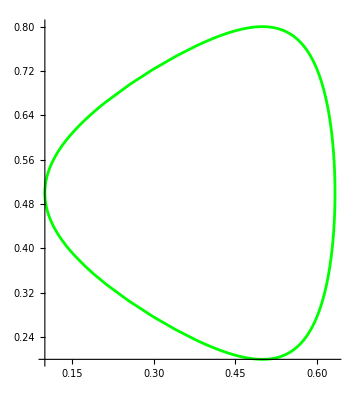

```mathematica
plotX=ParametricPlot[X[t],{t,0,1},PlotStyle->{Green}]
```

```mathematica
plotexact=ParametricPlot3D[{X[t][[1]],X[t][[2]],H[t]},{t,0,1},PlotStyle->{Blue}]
```

-Graphics3D-

```mathematica
plotnum=ListPointPlot3D[tt,PlotRange->Full,PlotStyle->{Red,PointSize->0.01}]
```

-Graphics3D-

```mathematica
Show[plotexact,plotnum,BoxRatios->{1,1,0.5}]
```

-Graphics3D-